```mathematica
CF1[re_]:=If[re<5*^5, 1.328/Sqrt[re],664000./re^1.5-36999.99999999999/re^1.2+0.074/re^0.19999999999999996]
```

```mathematica
B=rec*(0.074*re^(-0.2)-1.328*re^(-0.5))/.rec-> 5*^5
```

500000 (-1.328/re^0.5+0.074/re^0.2)

```mathematica
0.074*re^(-0.2)-B/re//Simplify
```

664000./re^1.5-37000./re^1.2+0.074/re^0.2

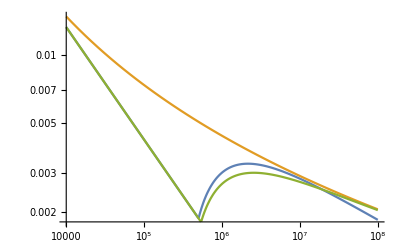

```mathematica
LogLogPlot[{CF1[re],CF2[re],CF3[re]},{re, 10^4,10^8}]
```

```mathematica
CF2[re_]:=(1.5*Log[re]-5.6)^(-2)
```

```mathematica
CF2[re]
```

1/(-5.6+1.5 Log[re])^2

```mathematica
CF3[re_]:=If[re<1*^4, 1.33*^-2, If[re<5.39*^5, 1.328/Sqrt[re],1/((1.50 *Log[re]-5.6)^2)-1700/re]]
```

```mathematica
CF3[re]
```

If[re<10000,0.0133,If[re<539000.,1.328/(√re),1/(1.5 Log[re]-5.6)^2-1700/re]]